Practical-2: Regula-Falsi Method
Name : - Ravikant Maurya
Roll No: 20221433
B.Sc. (Hons.) Computer Science

Regula-Falsi Method: For Given Parameters
Ques-1 : Cos[x]

x0= 1

x1= 2

Nmax= 10

epsilon= 0.001

f(x):=Cos[x]

1th iteration value is: 1.5649

estimate error is: 1.

2th iteration value is: 1.57098

estimate error is: 0.435096

3th iteration value is: 1.5708

estimate error is: 0.0060742

Return[1.5708]

root is: 1.5708

Estimate error is: 0.000182249

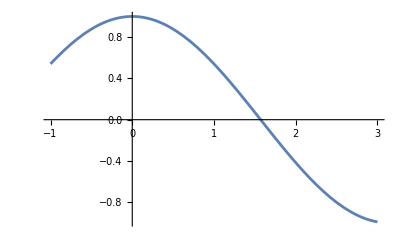

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x];
Print["f(x):=", f[x]];
If[N[f[x0]*f[x1]] > 0,
	Print["These values do not satisfy the IVP so change the values."],
	For[i=1, i<=Nmax, i++,
		x2 = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
		If[Abs[x1-x0] < eps, Return[N[x2]],
			Print[i, "th iteration value is: ", N[x2]];
			Print["estimate error is: ", N[x1-x0]]];
		If[f[x2]*f[x1] > 0, x1=x2, x0=x2]]];
Print["root is: ", N[x2]];
Print["Estimate error is: ", N[x1-x0]];
Plot[f[x], {x, -1, 3}]
```

Ques-2 : Cos[x]-x*e^x

x0= 1

x1= 2

Nmax= 19

epsilon= 0.001

f(x):=-ⅇ^x x+Cos[x]

These values do not satisfy the IVP so change the values.

root is: 1.5708

Estimate error is: 1.

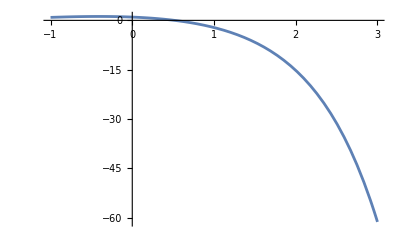

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := Cos[x] - x*ⅇ^x;
Print["f(x):=", f[x]];
If[N[f[x0]*f[x1]] > 0,
	Print["These values do not satisfy the IVP so change the values."],
	For[i=1, i<=Nmax, i++,
		x2 = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
		If[Abs[x1-x0] < eps, Return[N[x2]],
			Print[i, "th iteration value is: ", N[x2]];
			Print["estimate error is: ", N[x1-x0]]];
		If[f[x2]*f[x1] > 0, x1=x2, x0=x2]]];
Print["root is: ", N[x2]];
Print["Estimate error is: ", N[x1-x0]];
Plot[f[x], {x, -1, 3}]
```

Ques-3: x^3-5*x+1

x0= 1

x1= Null

Nmax= 20

epsilon= 0.001

f(x):=1-5 x+x^3

root is: 1.5708

Estimate error is: -1.+Null

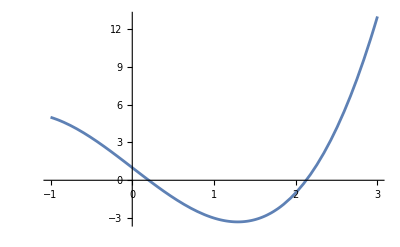

```mathematica
x0 = Input["Enter first guess :"];
x1 = Input["Enter second guess :"];
Nmax = Input["Enter maximum number of iteration :"];
eps = Input["Enter the value of convergence parameter :"];
Print["x0= ", x0];
Print["x1= ", x1];
Print["Nmax= ", Nmax];
Print["epsilon= ", eps];
f[x_] := x^3-5x+1;
Print["f(x):=", f[x]];
If[N[f[x0]*f[x1]] > 0,
	Print["These values do not satisfy the IVP so change the values."],
	For[i=1, i<=Nmax, i++,
		x2 = N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0])];
		If[Abs[x1-x0] < eps, Return[N[x2]],
			Print[i, "th iteration value is: ", N[x2]];
			Print["estimate error is: ", N[x1-x0]]];
		If[f[x2]*f[x1] > 0, x1=x2, x0=x2]]];
Print["root is: ", N[x2]];
Print["Estimate error is: ", N[x1-x0]];
Plot[f[x], {x, -1, 3}]
```